# Rabi cycling

## Optical Block equations for one laser field

H_0 = ℏω_0{{1,0},{0,0}}   
H_I[t]={{0,-μE[t]Cos[ωt]},{-μE[t]Cos[ωt],0}}
H_tot[t]=H_0+H_I[t]
ⅈℏ(∂ρ)/(∂t)=[H_tot,ρ]        ℏω_R=-μE[t]        ρ={{ρ_bb,ρ_ba},{ρ_ab,ρ_aa}}, a<-> Ground  State   ,   b <-> Excited  State

#### Derive the equations

```mathematica
Subscript[H, 0]=ℏbar Subscript[ω, 0]{{1,0},{0,0}};    Subscript[H, I]={{0,ℏbar Subscript[ω, R] Cos[ω t]},{ℏbar Subscript[ω, R] Cos[ω t],0}};   Subscript[H, tot]=Subscript[H, 0]+Subscript[H, I];       r={{Subscript[ρ, bb],Subscript[ρ, ba]},{Subscript[ρ, ab],Subscript[ρ, aa]}};        

RWA={Subscript[ρ, ba]-> Subscript[ρ, ba] ⅇ^(-ⅈ ω t),Subscript[ρ, ab]-> Subscript[ρ, ab] ⅇ^(ⅈ ω t),OverDot[Subscript[ρ, ba]]-> OverDot[Subscript[ρ, ba]] ⅇ^(-ⅈ ω t)-ⅈ ω Subscript[ρ, ba] ⅇ^(-ⅈ ω t),OverDot[Subscript[ρ, ab]]-> OverDot[Subscript[ρ, ab]] ⅇ^(ⅈ ω t)+ⅈ ω Subscript[ρ, ab] ⅇ^(ⅈ ω t)};
drdt=-ⅈ/ℏbar(Subscript[H, tot].r-r.Subscript[H, tot]);

FullSimplify[TrigToExp[drdt[[1,1]]-OverDot[Subscript[ρ, bb]]]/.RWA/.{ⅇ^(2 ⅈ  ω t)-> 0,ⅇ^(-2ⅈ ω t)-> 0}];
FullSimplify[TrigToExp[drdt[[2,2]]-OverDot[Subscript[ρ, aa]]]/.RWA/.{ⅇ^(2 ⅈ  ω t)-> 0,ⅇ^(-2ⅈ ω t)-> 0}];
FullSimplify[TrigToExp[drdt[[2,1]]-OverDot[Subscript[ρ, ab]]]/.RWA/.{ⅇ^(-ⅈ  ω t)-> 0,ⅇ^(ⅈ ω t)-> 1}];
FullSimplify[TrigToExp[drdt[[1,2]]]-OverDot[Subscript[ρ, ba]]/.RWA/.{ⅇ^(-ⅈ  ω t)-> 1,ⅇ^(ⅈ ω t)-> 0}];
```

## Two laser fields

H_0 = ℏω_0{{1,0},{0,0}}              
H_I[t]={{0,-μE_1[t]Cos[ω_1 t]-μE_2[t]Cos[ω_2 t]},{-μE_1[t]Cos[ω_1 t]-μE_2[t]Cos[ω_2 t],0}}
 H_tot[t]=H_0+H_I[t],          
ⅈℏ(∂ρ)/(∂t)=[H_tot,ρ] ,        ρ={{ρ_bb,ρ_ba},{ρ_ab,ρ_aa}}, a<-> Ground  State   ,b<-> Excited  State

#### Derive the equations

```mathematica
Subscript[H, 0]= ℏbar Subscript[ω, 0]{{1,0},{0,0}};  
Subscript[H, I][t]={{0,-Subscript[μE, 1][t]Cos[Subscript[ω, 1] t]-Subscript[μE, 2][t]Cos[Subscript[ω, 2] t]},{-Subscript[μE, 1][t]Cos[Subscript[ω, 1] t]-Subscript[μE, 2][t]Cos[Subscript[ω, 2] t],0}};
Subscript[H, Tot][t]=Subscript[H, 0]+Subscript[H, I][t];
r={{Subscript[ρ, bb],Subscript[ρ, ba]},{Subscript[ρ, ab],Subscript[ρ, aa]}}; 
RWA={Subscript[ρ, ba]-> Subscript[ρ, ba] ⅇ^(-ⅈ Subscript[ω, 1] t),Subscript[ρ, ab]-> Subscript[ρ, ab] ⅇ^(ⅈ Subscript[ω, 1] t),OverDot[Subscript[ρ, ba]]-> OverDot[Subscript[ρ, ba]] ⅇ^(-ⅈ Subscript[ω, 1] t)-ⅈ Subscript[ω, 1] Subscript[ρ, ba] ⅇ^(-ⅈ Subscript[ω, 1] t),OverDot[Subscript[ρ, ab]]-> OverDot[Subscript[ρ, ab]] ⅇ^(ⅈ Subscript[ω, 1] t)+ⅈ Subscript[ω, 1] Subscript[ρ, ab] ⅇ^(ⅈ Subscript[ω, 1] t)};
drdt=-ⅈ/ℏbar(Subscript[H, Tot][t].r-r.Subscript[H, Tot][t]);

FullSimplify[TrigToExp[drdt[[1,1]]-OverDot[Subscript[ρ, bb]]]/.RWA/.{ⅇ^(2 ⅈ  Subscript[ω, 1] t)-> 0,ⅇ^(-2ⅈ Subscript[ω, 1] t)-> 0}];
FullSimplify[TrigToExp[drdt[[2,2]]-OverDot[Subscript[ρ, aa]]]/.RWA/.{ⅇ^(2 ⅈ  Subscript[ω, 1] t)-> 0,ⅇ^(-2ⅈ Subscript[ω, 1] t)-> 0}];
FullSimplify[TrigToExp[drdt[[2,1]]-OverDot[Subscript[ρ, ab]]]/.RWA/.{ⅇ^(-ⅈ  Subscript[ω, 1] t)-> 0,ⅇ^(ⅈ Subscript[ω, 1] t)-> 1}];
FullSimplify[TrigToExp[drdt[[1,2]]]-OverDot[Subscript[ρ, ba]]/.RWA/.{ⅇ^(-ⅈ  Subscript[ω, 1] t)-> 1,ⅇ^(ⅈ Subscript[ω, 1] t)-> 0}];

FullSimplify[TrigToExp[drdt[[1,1]]-OverDot[Subscript[ρ, bb]]]/.RWA];
FullSimplify[TrigToExp[drdt[[2,2]]-OverDot[Subscript[ρ, aa]]]/.RWA];
FullSimplify[(TrigToExp[drdt[[2,1]]-OverDot[Subscript[ρ, ab]]])*ⅇ^(-ⅈ t Subscript[ω, 1])/.RWA]/.{ⅇ^(-ⅈ Subscript[ω, 1] t)-> 1,Cos[Subscript[ω, 1] t]-> 1/2,Cos[Subscript[ω, 2] t]-> ⅇ^(-ⅈ (Subscript[ω, 1]-Subscript[ω, 2] )t)/2};
FullSimplify[(TrigToExp[drdt[[1,2]]-OverDot[Subscript[ρ, ba]]])*ⅇ^(ⅈ t Subscript[ω, 1])/.RWA]/.{ⅇ^(ⅈ Subscript[ω, 1] t)-> 1,Cos[Subscript[ω, 1] t]-> 1/2,Cos[Subscript[ω, 2] t]->ⅇ^(ⅈ (Subscript[ω, 1]-Subscript[ω, 2] )t)/2};
```

## Solve the equations

#### Constants and functions

```mathematica
ϵ=8.854187817 10^-12; (* Subscript[ϵ, 0] [J/V^2 m] *)   
c=2.99792458 10^8;      (* [m/s] *)
ℏ=1.055 10^-34;             (* [J*s] *)
kB=1.38065 10^-23;      (* Boltzmann constant [J/K] *)

AbsEl[x_,y_,z_,power_,wzero_,λ_,x0_,y0_,z0_]=2 √(power/(π ϵ c wzero^2)) wzero/(wzero √(1+(((y-y0)λ)/(π wzero^2))^2))ⅇ^(-(((z-z0)^2+(x-x0)^2)/((wzero √(1+(((y-y0)λ)/(π wzero^2))^2))^2)));
PhaseEl[x_,y_,z_,wzero_,λ_,x0_,y0_,z0_]=-(2π)/λ(y-y0)-(2π)/λ((z-z0)^2+(x-x0)^2)/(2 (y-y0) (1+((π wzero^2)/((y-y0)λ))^2))+ArcTan[(y-y0)/((π wzero^2)/λ)];
```

#### Setup parameters

```mathematica
z0=-70000.0;x0=-161.36013;y0=255.99043;    vz=333.05538;vx=-0.14633;vy=0.06014; vel={vx,vy,vz};
x[t_]=x0+vx (t+210.30976);y[t_]=y0+vy (t+210.30976);z[t_]=z0+vz (t+210.30976);

Subscript[t, in]=370;    Subscript[t, fin]=470;

power1=0.01;(* first QCL power [W] *)     power2=0.01;(* second QCL power [W] *)
wzero1=1250;(* first QCL waist [μm] *)                   wzero2=1250;(* second QCL waist [μm] *)
λ1=5.8326;(* first QCL wavelenght [μm] *)                                     λ2=5.8326;(* second QCL wavelenght [μm] *)
z01=131800.0; x01=0; y01=830000.0;                 z02=138800.0+0; x02=0; y02=830000.0;     (* first and second laser focal spot positions [μm] *)
Subscript[ω, 0]=2π*51399115.447000;      (* angular frequency for the molecular transition a^3 Subscript[Π, 1]: v=0 -> v=1 *)
Subscript[ω, 1]=2π*51399115.447000;   Subscript[ω, 2]=2π*51399115.447000;   (*  first and second QCL angular frequencies [MHz] *)
Debye=3.336 10^-30;(* [C*m] *)
μ=0.05 Debye 10^6;(* matrix element between states connected by the QCL (v=0 -> v=1) [C*μm] *)

ElTime1[t_]=AbsEl[x[t],y[t],z[t],power1,wzero1,λ1,x01,y01,z01];
ElTime2[t_]=AbsEl[x[t],y[t],z[t],power2,wzero2,λ2,x02,y02,z02];
PhaseTime1[t_]=PhaseEl[x[t],y[t],z[t],wzero1,λ1,x01,y01,z01];
PhaseTime2[t_]=PhaseEl[x[t],y[t],z[t],wzero2,λ2,x02,y02,z02];
Subscript[ω, R1][t_]=(μ ElTime1[t])/ℏ 10^-6;   Subscript[ω, R2][t_]=(μ ElTime2[t])/ℏ 10^-6;  (*Rabi frequencies [MHz] *)
Subscript[Δ, 1][t_]=Subscript[ω, 1]-Subscript[ω, 0]+Dt[PhaseTime1[t],t];
Subscript[Δ, 2][t_]=Subscript[ω, 2]-Subscript[ω, 0]+Dt[PhaseTime2[t],t];
Subscript[Δ, 12][t_]=Subscript[ω, 1]-Subscript[ω, 2]+Dt[PhaseTime1[t],t]-Dt[PhaseTime2[t],t];
```

#### Numerical integration

Regarding the spontaneous emission we implemented the following master equation:   ∂/∂tρ=-i [ω_R σ^++ω_R^*σ^-,ρ] + Γ/2(2 BR σ^- ρ σ^+-σ^+σ^- ρ -ρ σ^+σ^- )

```mathematica
BR=0;                     (* Branching ratio of decayments from the excited state Subscript[ρ, bb] towards the ground state Subscript[ρ, aa] *)
TimeLife= 2600;       (* time life [μs] *)
Γ=1/TimeLife;        (* decay rate [MHz] to be compared to Rabi frequency*)

OneLaser=NDSolve[{Subscript[ρ, bb]'[t]==ⅈ/2 Subscript[ω, R1][t]( Subscript[ρ, ba][t]-Subscript[ρ, ab][t]),   Subscript[ρ, aa]'[t]==-ⅈ/2 Subscript[ω, R1][t]( Subscript[ρ, ba][t]-Subscript[ρ, ab][t]),
Subscript[ρ, ab]'[t]==-ⅈ Subscript[Δ, 1][t]Subscript[ρ, ab][t]-ⅈ/2 Subscript[ω, R1][t] (Subscript[ρ, bb][t]-Subscript[ρ, aa][t]),   Subscript[ρ, ba]'[t]==ⅈ Subscript[Δ, 1][t]Subscript[ρ, ba][t]+ⅈ/2 Subscript[ω, R1][t] (Subscript[ρ, bb][t]-Subscript[ρ, aa][t]),
 Subscript[ρ, bb][Subscript[t, in]]==0,Subscript[ρ, aa][Subscript[t, in]]==1, Subscript[ρ, ab][Subscript[t, in]]==0 ,Subscript[ρ, ba][Subscript[t, in]]==0},{Subscript[ρ, bb][t],Subscript[ρ, aa][t],Subscript[ρ, ab][t] ,Subscript[ρ, ba][t]},{t,Subscript[t, in],Subscript[t, fin]},MaxSteps->10^5];
SpontaneousEmission=NDSolve[{Subscript[ρ, bb]'[t]==ⅈ/2 Subscript[ω, R1][t]( Subscript[ρ, ba][t]-Subscript[ρ, ab][t])-Γ*Subscript[ρ, bb][t],   Subscript[ρ, aa]'[t]==-ⅈ/2 Subscript[ω, R1][t]( Subscript[ρ, ba][t]-Subscript[ρ, ab][t])+BR*Γ*Subscript[ρ, bb][t],
Subscript[ρ, ab]'[t]==-ⅈ Subscript[Δ, 1][t]Subscript[ρ, ab][t]-ⅈ/2 Subscript[ω, R1][t] (Subscript[ρ, bb][t]-Subscript[ρ, aa][t])-Γ/2*Subscript[ρ, ab][t],   Subscript[ρ, ba]'[t]==ⅈ Subscript[Δ, 1][t]Subscript[ρ, ba][t]+ⅈ/2 Subscript[ω, R1][t] (Subscript[ρ, bb][t]-Subscript[ρ, aa][t])-Γ/2*Subscript[ρ, ba][t],
 Subscript[ρ, bb][Subscript[t, in]]==0,Subscript[ρ, aa][Subscript[t, in]]==1, Subscript[ρ, ab][Subscript[t, in]]==0 ,Subscript[ρ, ba][Subscript[t, in]]==0},{Subscript[ρ, bb][t],Subscript[ρ, aa][t],Subscript[ρ, ab][t] ,Subscript[ρ, ba][t]},{t,Subscript[t, in],Subscript[t, fin]},MaxSteps->10^5];

TwoLasers=NDSolve[{Subscript[ρ, bb]'[t]==ⅈ/2 Subscript[ω, R1][t]( Subscript[ρ, ba][t]-Subscript[ρ, ab][t])+ⅈ/2 Subscript[ω, R2][t](ⅇ^(-ⅈ Subscript[Δ, 12][t]t) Subscript[ρ, ba][t]-ⅇ^(ⅈ Subscript[Δ, 12][t]t)Subscript[ρ, ab][t]),   Subscript[ρ, aa]'[t]==-ⅈ/2 Subscript[ω, R1][t]( Subscript[ρ, ba][t]-Subscript[ρ, ab][t])-ⅈ/2 Subscript[ω, R2][t](ⅇ^(-ⅈ Subscript[Δ, 12][t]t) Subscript[ρ, ba][t]-ⅇ^(ⅈ Subscript[Δ, 12][t]t)Subscript[ρ, ab][t]),
 Subscript[ρ, ab]'[t]==-ⅈ Subscript[Δ, 1][t]Subscript[ρ, ab][t]-ⅈ/2 Subscript[ω, R1][t] (Subscript[ρ, bb][t]-Subscript[ρ, aa][t])-ⅈ/2 Subscript[ω, R2][t] ⅇ^(-ⅈ Subscript[Δ, 12][t]t) (Subscript[ρ, bb][t]-Subscript[ρ, aa][t]),   Subscript[ρ, ba]'[t]==ⅈ Subscript[Δ, 1][t]Subscript[ρ, ba][t]+ⅈ/2 Subscript[ω, R1][t] (Subscript[ρ, bb][t]-Subscript[ρ, aa][t])+ⅈ/2 Subscript[ω, R2][t] ⅇ^(+ⅈ Subscript[Δ, 12][t]t) (Subscript[ρ, bb][t]-Subscript[ρ, aa][t]),
 Subscript[ρ, bb][Subscript[t, in]]==0,Subscript[ρ, aa][Subscript[t, in]]==1, Subscript[ρ, ab][Subscript[t, in]]==0,Subscript[ρ, ba][Subscript[t, in]]==0},{Subscript[ρ, bb][t],Subscript[ρ, aa][t],Subscript[ρ, ab][t],Subscript[ρ, ba][t]},{t,Subscript[t, in],Subscript[t, fin]},MaxSteps->10^5];
```

#### Plots

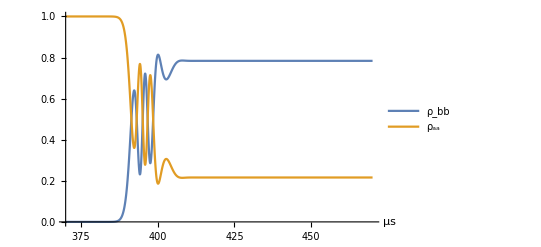

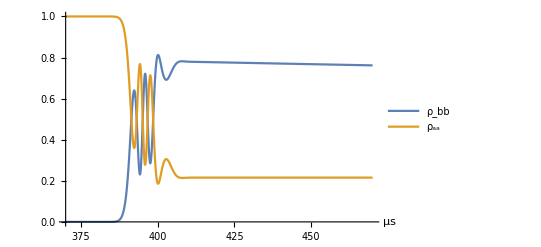

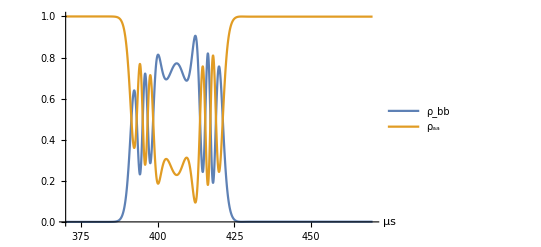

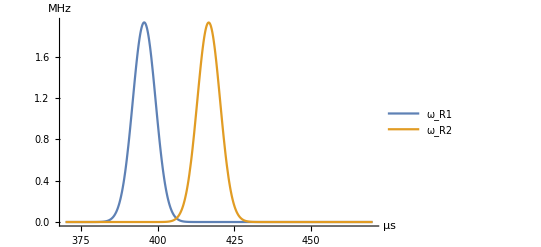

```mathematica
pr={{Subscript[t, in],Subscript[t, fin]},{0,1}};
Plot[{Subscript[ρ, bb][t]/.OneLaser,Subscript[ρ, aa][t]/.OneLaser},{t,Subscript[t, in],Subscript[t, fin]},PlotRange->pr,AxesLabel->{μs},PlotLegends->{Subscript[ρ, bb],Subscript[ρ, aa]}]
Plot[{Subscript[ρ, bb][t]/.SpontaneousEmission,Subscript[ρ, aa][t]/.SpontaneousEmission},{t,Subscript[t, in],Subscript[t, fin]},PlotRange->pr,AxesLabel->{μs},PlotLegends->{Subscript[ρ, bb],Subscript[ρ, aa]}]
Plot[{Subscript[ρ, bb][t]/.TwoLasers,Subscript[ρ, aa][t]/.TwoLasers},{t,Subscript[t, in],Subscript[t, fin]},PlotRange->pr,AxesLabel->{μs},PlotLegends->{Subscript[ρ, bb],Subscript[ρ, aa]}]
Plot[{Subscript[ω, R1][t],Subscript[ω, R2][t]},{t,Subscript[t, in],Subscript[t, fin]},PlotRange->All,AxesLabel->{μs,MHz},PlotLegends->{Subscript[ω, R1],Subscript[ω, R2]}]
```